This notebook calculates the relation between radius and pressure at the RCB by interating hydrostating balance.  The radiative zone is assumed to be non-selfgravitating ideal gas with powerlaw opacity.  Details of the calculation are in CoreAccretion.tex as is a table of values.  The results of the calculation are expressed in terms of a deviation from the result for an isothermal radiative zone.

## Pressure Radius Relation at Convective Boundary

### Direct integration

```mathematica
Quit
```

```mathematica
α = 0; β = 3/4;Δ = 2/7;
Δ∞ = (1+α)/(4-β)
cΔ = 1/(Δ∞/Δ-1)
```

4/13

13

```mathematica
int = Assuming[0<ϵ< 1,Integrate[(1+cΔ ϵ^(1+α)(p^(1+α)-1))^(1/(4-β))/p,{p,1,1/ϵ}]]
```

1/4 (-13+13 (14-13 ϵ)^(4/13)+4 (-1)^(7/26) (-1+13 ϵ)^(4/13) ArcTan[(-ⅈ+(-1)^(23/26)-13 (-ⅈ+(-1)^(23/26)) ϵ+2 (-1)^(5/26) (-1+13 ϵ)^(12/13))/((1+(-1)^(5/13)) (-1+13 ϵ))]-4 (-1)^(19/26) (-1+13 ϵ)^(4/13) ArcTan[(-ⅈ+(-1)^(23/26)-13 (-ⅈ+(-1)^(23/26)) ϵ+2 (-1)^(5/26) (-1+13 ϵ)^(12/13))/((1+(-1)^(5/13)) (-1+13 ϵ))]-4 (-1)^(7/26) (-1+13 ϵ)^(4/13) ArcTan[(-ⅈ+(-1)^(23/26)-13 (-ⅈ+(-1)^(23/26)) ϵ+2 (-1)^(5/26) (14-13 ϵ)^(1/13) (-1+13 ϵ)^(12/13))/((1+(-1)^(5/13)) (-1+13 ϵ))]+4 (-1)^(19/26) (-1+13 ϵ)^(4/13) ArcTan[(-ⅈ+(-1)^(23/26)-13 (-ⅈ+(-1)^(23/26)) ϵ+2 (-1)^(5/26) (14-13 ϵ)^(1/13) (-1+13 ϵ)^(12/13))/((1+(-1)^(5/13)) (-1+13 ϵ))]+4 (-1)^(5/26) (-1+13 ϵ)^(4/13) ArcTan[Cot[π/13]-Csc[π/13]/((1-13 ϵ)/(-14+13 ϵ))^(1/13)]-4 (-1)^(21/26) (-1+13 ϵ)^(4/13) ArcTan[Cot[π/13]-Csc[π/13]/((1-13 ϵ)/(-14+13 ϵ))^(1/13)]-4 (-1)^(5/26) (-1+13 ϵ)^(4/13) ArcTan[Cot[π/13]-Csc[π/13]/(-1+13 ϵ)^(1/13)]+4 (-1)^(21/26) (-1+13 ϵ)^(4/13) ArcTan[Cot[π/13]-Csc[π/13]/(-1+13 ϵ)^(1/13)]-4 (-1)^(9/26) (-1+13 ϵ)^(4/13) ArcTan[Sec[π/26]/((1-13 ϵ)/(-14+13 ϵ))^(1/13)+Tan[π/26]]+4 (-1)^(17/26) (-1+13 ϵ)^(4/13) ArcTan[Sec[π/26]/((1-13 ϵ)/(-14+13 ϵ))^(1/13)+Tan[π/26]]+4 (-1)^(9/26) (-1+13 ϵ)^(4/13) ArcTan[Sec[π/26]/(-1+13 ϵ)^(1/13)+Tan[π/26]]-4 (-1)^(17/26) (-1+13 ϵ)^(4/13) ArcTan[Sec[π/26]/(-1+13 ϵ)^(1/13)+Tan[π/26]]-4 (-1)^(3/26) (-1+13 ϵ)^(4/13) ArcTan[1/2 (-Cot[π/13]-(Csc[π/13] Sec[π/13])/((1-13 ϵ)/(-14+13 ϵ))^(1/13)+Tan[π/13])]+4 (-1)^(23/26) (-1+13 ϵ)^(4/13) ArcTan[1/2 (-Cot[π/13]-(Csc[π/13] Sec[π/13])/((1-13 ϵ)/(-14+13 ϵ))^(1/13)+Tan[π/13])]+4 (-1)^(3/26) (-1+13 ϵ)^(4/13) ArcTan[1/2 (-Cot[π/13]-(Csc[π/13] Sec[π/13])/(-1+13 ϵ)^(1/13)+Tan[π/13])]-4 (-1)^(23/26) (-1+13 ϵ)^(4/13) ArcTan[1/2 (-Cot[π/13]-(Csc[π/13] Sec[π/13])/(-1+13 ϵ)^(1/13)+Tan[π/13])]+4 (-1)^(1/13) (1+(-1)^(11/13)) (-1+13 ϵ)^(4/13) ArcTanh[(1+(-1)^(6/13)-13 (1+(-1)^(6/13)) ϵ+2 (-1)^(3/13) (-1+13 ϵ)^(12/13))/((-1+(-1)^(6/13)) (-1+13 ϵ))]+4 (-1)^(6/13) (1+(-1)^(1/13)) (-1+13 ϵ)^(4/13) ArcTanh[(-1+(-1)^(3/13)-13 (-1+(-1)^(3/13)) ϵ+2 (-1)^(8/13) (-1+13 ϵ)^(12/13))/((1+(-1)^(3/13)) (-1+13 ϵ))]-4 (-1)^(1/13) (1+(-1)^(11/13)) (-1+13 ϵ)^(4/13) ArcTanh[(1+(-1)^(6/13)-13 (1+(-1)^(6/13)) ϵ+2 (-1)^(3/13) (14-13 ϵ)^(1/13) (-1+13 ϵ)^(12/13))/((-1+(-1)^(6/13)) (-1+13 ϵ))]-4 (-1)^(6/13) (1+(-1)^(1/13)) (-1+13 ϵ)^(4/13) ArcTanh[(-1+(-1)^(3/13)-13 (-1+(-1)^(3/13)) ϵ+2 (-1)^(8/13) (14-13 ϵ)^(1/13) (-1+13 ϵ)^(12/13))/((1+(-1)^(3/13)) (-1+13 ϵ))]-4 (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(1/13)]+4 (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(1/13)+(-1+13 ϵ)^(1/13)]+2 (-1)^(3/13) (-1+13 ϵ)^(4/13) Log[1+(-1)^(4/13) (-1+13 ϵ)^(1/13)-(-1)^(9/13) (-1+13 ϵ)^(1/13)+(-1+13 ϵ)^(2/13)]-2 (-1)^(10/13) (-1+13 ϵ)^(4/13) Log[1+(-1)^(4/13) (-1+13 ϵ)^(1/13)-(-1)^(9/13) (-1+13 ϵ)^(1/13)+(-1+13 ϵ)^(2/13)]-2 (-1)^(3/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)+(-1)^(4/13) ((14-13 ϵ) (-1+13 ϵ))^(1/13)-(-1)^(9/13) ((14-13 ϵ) (-1+13 ϵ))^(1/13)]+2 (-1)^(10/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)+(-1)^(4/13) ((14-13 ϵ) (-1+13 ϵ))^(1/13)-(-1)^(9/13) ((14-13 ϵ) (-1+13 ϵ))^(1/13)]-2 (-1)^(4/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)-2 (-1+13 ϵ)^(1/13) Cos[π/13]]+2 (-1)^(9/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)-2 (-1+13 ϵ)^(1/13) Cos[π/13]]+2 (-1)^(4/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)-2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13]]-2 (-1)^(9/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)-2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13]]-2 (-1)^(2/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)+2 (-1+13 ϵ)^(1/13) Sin[π/26]]+2 (-1)^(11/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)+2 (-1+13 ϵ)^(1/13) Sin[π/26]]+2 (-1)^(2/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)+2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Sin[π/26]]-2 (-1)^(11/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)+2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Sin[π/26]]-2 (-1)^(6/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)-6 (-1+13 ϵ)^(1/13) Cos[π/26]^2 Sin[π/26]+2 (-1+13 ϵ)^(1/13) Sin[π/26]^3]+2 (-1)^(7/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)-6 (-1+13 ϵ)^(1/13) Cos[π/26]^2 Sin[π/26]+2 (-1+13 ϵ)^(1/13) Sin[π/26]^3]+2 (-1)^(6/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)-6 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/26]^2 Sin[π/26]+2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Sin[π/26]^3]-2 (-1)^(7/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)-6 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/26]^2 Sin[π/26]+2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Sin[π/26]^3]+2 (-1)^(5/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)+2 (-1+13 ϵ)^(1/13) Cos[π/13]^2-2 (-1+13 ϵ)^(1/13) Sin[π/13]^2]-2 (-1)^(8/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)+2 (-1+13 ϵ)^(1/13) Cos[π/13]^2-2 (-1+13 ϵ)^(1/13) Sin[π/13]^2]-2 (-1)^(5/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)+2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13]^2-2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Sin[π/13]^2]+2 (-1)^(8/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)+2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13]^2-2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Sin[π/13]^2]+2 (-1)^(1/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)-2 (-1+13 ϵ)^(1/13) Cos[π/13]^3+6 (-1+13 ϵ)^(1/13) Cos[π/13] Sin[π/13]^2]-2 (-1)^(12/13) (-1+13 ϵ)^(4/13) Log[1+(-1+13 ϵ)^(2/13)-2 (-1+13 ϵ)^(1/13) Cos[π/13]^3+6 (-1+13 ϵ)^(1/13) Cos[π/13] Sin[π/13]^2]-2 (-1)^(1/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)-2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13]^3+6 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13] Sin[π/13]^2]+2 (-1)^(12/13) (-1+13 ϵ)^(4/13) Log[(14-13 ϵ)^(2/13)+(-1+13 ϵ)^(2/13)-2 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13]^3+6 ((14-13 ϵ) (-1+13 ϵ))^(1/13) Cos[π/13] Sin[π/13]^2])

```mathematica
lim = Limit[N[Re[int]+Log[ϵ]],ϵ-> 0]
```

1.9308

```mathematica
N[lim]
Exp[-lim]
```

1.9308

0.145032

#### β = 2 case

```mathematica
α = 0; β = 2;Δ = 2/7;
Δ∞ = (1+α)/(4-β)
cΔ = 1/(Δ∞/Δ-1)
```

1/2

4/3

```mathematica
int = Assuming[0<ϵ< 1,Integrate[(1+cΔ ϵ^(1+α)(p^(1+α)-1))^(1/(4-β))/p,{p,1,1/ϵ}]]
```

2/3 (-3+√3 √(7-4 ϵ)+√(-9+12 ϵ) ArcTan[1/(√(-1+(4 ϵ)/3))]-√(-9+12 ϵ) ArcTan[1/(√((3-4 ϵ)/(-7+4 ϵ)))])

```mathematica
lim = Limit[Re[int]+Log[ϵ],ϵ-> 0]
```

-2+2 √(7/3)+Log[3]+1/2 Log[5-√21]-1/2 Log[5+√21]

```mathematica
N[lim]
Exp[-N[lim]]
```

0.586864

0.556069

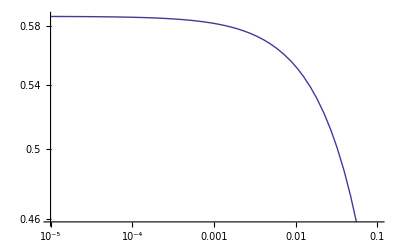

```mathematica
LogLogPlot[{int+ Log[ϵ]},{ϵ,1*^-5,.1}]
```

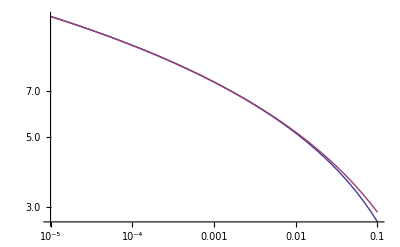

```mathematica
LogLogPlot[{int,(-2+2 √(7/3)+Log[6]-Log[(5+√21) ϵ])},{ϵ,1*^-5,.1}]
```

#### β = 1 case

```mathematica
Quit
```

```mathematica
α = 0; β = 1;Δ = 2/7;
Δo = (1+α)/(4-β)
cΔ = 1/(Δo/Δ-1)
```

1/3

6

```mathematica
Clear[ϵ]
```

```mathematica
int = Assuming[0<ϵ< 1,Integrate[(1+cΔ ϵ(p-1))^(1/(4-β))/p,{p,1,1/ϵ}]]
```

-3+3 (7-6 ϵ)^(1/3)-√3 (-1+6 ϵ)^(1/3) ArcTan[(1-2/(-1+6 ϵ)^(1/3))/(√3)]+√3 (-1+6 ϵ)^(1/3) ArcTan[(1-(2 (7-6 ϵ)^(1/3))/(-1+6 ϵ)^(1/3))/(√3)]+(-1+6 ϵ)^(1/3) Log[1+(-1+6 ϵ)^(1/3)]-(-1+6 ϵ)^(1/3) Log[(7-6 ϵ)^(1/3)+(-1+6 ϵ)^(1/3)]-1/2 (-1+6 ϵ)^(1/3) Log[1-(-1+6 ϵ)^(1/3)+(-1+6 ϵ)^(2/3)]+1/2 (-1+6 ϵ)^(1/3) Log[(7-6 ϵ)^(2/3)+(-1+6 ϵ)^(2/3)-(-7+48 ϵ-36 ϵ^2)^(1/3)]

```mathematica
lim = Limit[N[int+Log[ϵ]], ϵ-> 0]
Exp[-lim]
```

1.25238

0.285824

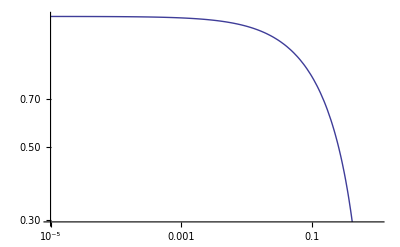

```mathematica
LogLogPlot[{Re[int] + Log[ϵ] },{ϵ,1*^-5,1}]
```

Analytic Limit is

```mathematica
Limit[int+Log[ϵ], ϵ-> 0]
```

Limit::ztest: Unable to decide whether numeric quantities {1 - ⅇ^ⅈ\ π/3 + ⅇ^2\ ⅈ\ π/3, -ⅈ + 1/√3 + 2\ ⅇ^2\ ⅈ\ π/3/√3, -ⅇ^ⅈ\ π/6 + √3\ ⅇ^2\ ⅈ\ π/3 - 2\ ⅇ^5\ ⅈ\ π/6, 2\ ⅇ^ⅈ\ π/6 - 2\ √3\ ⅇ^2\ ⅈ\ π/3 + 4\ ⅇ^5\ ⅈ\ π/6} are equal to zero. Assuming they are.

1/4 (-12+12 7^(1/3)+2 (3 ⅈ+√3) ArcTan[(1+2 (-1)^(2/3) 7^(1/3))/(√3)]-ⅈ √3 Log[2]+Log[8]+2 Log[1+(-1)^(1/3)]+2 ⅈ √3 Log[1+(-1)^(1/3)]-3 Log[-2-(2 ⅈ)/(√3)]+ⅈ √3 Log[-2-(2 ⅈ)/(√3)]-Log[3-ⅈ √3]-ⅈ √3 Log[3-ⅈ √3]-2 Log[(-1)^(1/3)+7^(1/3)]-2 ⅈ √3 Log[(-1)^(1/3)+7^(1/3)]+Log[-(-7)^(1/3)+(-1)^(2/3)+7^(2/3)]+ⅈ √3 Log[-(-7)^(1/3)+(-1)^(2/3)+7^(2/3)])

```mathematica
FullSimplify[%10]
```

1/4 (-12+12 7^(1/3)+(2 ⅈ+4/(√3)) π+2 (3 ⅈ+√3) ArcTan[(1+Root[-56+#1^3&,3])/(√3)]+(1+ⅈ √3) Log[-(4 (-(-7)^(1/3)+(-1)^(2/3)+7^(2/3)))/((1+2 7^(1/3))^2)]+Log[9/16 (1+(ⅈ √3)/(1+2 7^(1/3)))^(-2-2 ⅈ √3)])

```mathematica
Re[%16]
```

-3+3 7^(1/3)+π/(√3)+1/4 Re[2 (3 ⅈ+√3) ArcTan[(1+Root[-56+#1^3&,3])/(√3)]+(1+ⅈ √3) Log[-(4 (-(-7)^(1/3)+(-1)^(2/3)+7^(2/3)))/((1+2 7^(1/3))^2)]+Log[9/16 (1+(ⅈ √3)/(1+2 7^(1/3)))^(-2-2 ⅈ √3)]]

### Direct integration with Helium

#### β = 2 case

Gives c = 0.6564
Exp[c] = 1.93

```mathematica
α = 0; β = 2;Δ = 0.3008849557522124;
Δo = (1+α)/(4-β);
cΔ = 1/(Δo/Δ-1)
```

1.51111

```mathematica
int = Assuming[0<ϵ< 1,Integrate[(1+cΔ ϵ^(1+α)(p^(1+α)-1))^(1/(4-β))/p,{p,1,1/ϵ}]]
```

-2.+2. √(2.51111-1.51111 ϵ)+√(1.-1.51111 ϵ) (1. Log[1.-1./(√(1.-1.51111/(2.51111-1.51111 ϵ)))]-1. Log[1.+1./(√(1.-1.51111/(2.51111-1.51111 ϵ)))]-1. Log[1.-1./(√(1.-1.51111 ϵ))]+1. Log[1.+1./(√(1.-1.51111 ϵ))])

```mathematica
Assuming[0<ϵ<1/100,FullSimplify[Series[int,{ϵ,0,0}]]]
```

((0.656412+0. ⅈ)-1. Log[ϵ])+O[ϵ]^1

```mathematica
c = 0.6564124111147804;
Exp[c]
```

1.92786

```mathematica
Exp[-0.586863514999592]
```

0.556069

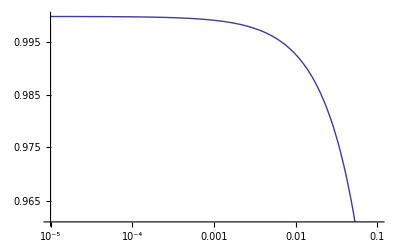

```mathematica
LogLogPlot[{int/(c-Log[ϵ])},{ϵ,1*^-5,.1}]
```

#### β = 1 case

Gives c = 1.70488
Exp[c] = 5.50

```mathematica
Exp[1.704]
```

5.49589

```mathematica
Quit
```

```mathematica
Δ
```

0.300885

```mathematica
α = 0; β = 1;Δ = 0.3008849557522124;
Δo = (1+α)/(4-β)
cΔ = 1/(Δo/Δ-1)
```

1/3

9.27273

```mathematica
nϵ = 100;
ϵarr = Table[10^-7 10^(6.(i-1)/(nϵ-1)),{i,nϵ}];
intarr = Table[NIntegrate[(1+cΔ ϵarr[[i]]^(1+α)(p^(1+α)-1))^(1/(4-β))/p,{p,1,1/ϵarr[[i]]}],{i,nϵ}];
```

```mathematica
intplot = Table[{ϵarr[[i]],intarr[[i]]},{i,nϵ}];
```

{{1.×10^-7,1.70488},{1.14976×10^-7,1.70488},{1.32194×10^-7,1.70488},{1.51991×10^-7,1.70488},{1.74753×10^-7,1.70488},{2.00923×10^-7,1.70488},{2.31013×10^-7,1.70488},{2.65609×10^-7,1.70488},{3.05386×10^-7,1.70487},{3.51119×10^-7,1.70487},{4.03702×10^-7,1.70487},{4.64159×10^-7,1.70487},{5.3367×10^-7,1.70486},{6.13591×10^-7,1.70486},{7.0548×10^-7,1.70486},{8.11131×10^-7,1.70485},{9.32603×10^-7,1.70485},{1.07227×10^-6,1.70484},{1.23285×10^-6,1.70484},{1.41747×10^-6,1.70483},{1.62975×10^-6,1.70482},{1.87382×10^-6,1.70482},{2.15443×10^-6,1.70481},{2.47708×10^-6,1.70479},{2.84804×10^-6,1.70478},{3.27455×10^-6,1.70477},{3.76494×10^-6,1.70475},{4.32876×10^-6,1.70473},{4.97702×10^-6,1.70471},{5.72237×10^-6,1.70469},{6.57933×10^-6,1.70466},{7.56463×10^-6,1.70463},{8.69749×10^-6,1.7046},{0.00001,1.70456},{0.0000114976,1.70451},{0.0000132194,1.70446},{0.0000151991,1.7044},{0.0000174753,1.70434},{0.0000200923,1.70427},{0.0000231013,1.70418},{0.0000265609,1.70409},{0.0000305386,1.70398},{0.0000351119,1.70386},{0.0000403702,1.70373},{0.0000464159,1.70357},{0.000053367,1.7034},{0.0000613591,1.7032},{0.000070548,1.70298},{0.0000811131,1.70273},{0.0000932603,1.70245}}

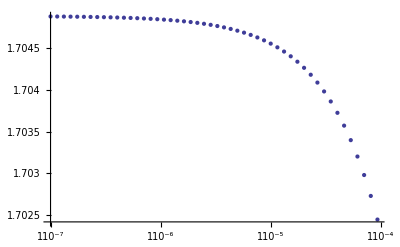

```mathematica
intfit = Table[{ϵarr[[i]],intarr[[i]]+ Log[ϵarr[[i]]]},{i,50}]
ListLogLogPlot[intfit]
```

```mathematica
ϵ = 10^-5;
NIntegrate[(1+cΔ ϵ^(1+α)(p^(1+α)-1))^(1/(4-β))/p,{p,1,1/ϵ}]
```

13.2175

```mathematica
Clear[ϵ]
```

Analytic integration doesn’t work so good.

```mathematica
int = Assuming[0<ϵ< 1/10,Integrate[(1+cΔ ϵ^(1+α)(p^(1+α)-1))^(1/(4-β))/p,{p,1,1/ϵ}]]
```

-3.+30.8182/(10.2727-9.27273 ϵ)^(2/3)-(27.8182 ϵ)/(10.2727-9.27273 ϵ)^(2/3)+(-0.339849+3.15133 ϵ) Hypergeometric2F1[0.666667,0.666667,1.66667,-0.107843+ϵ]+(-1.33414×10^-17+1.23711×10^-16 ϵ) Hypergeometric2F1[1.66667,1.66667,2.66667,-0.107843+ϵ]-1.02294×10^-33 Hypergeometric2F1[2.66667,2.66667,3.66667,-0.107843+ϵ]+9.48541×10^-33 ϵ Hypergeometric2F1[2.66667,2.66667,3.66667,-0.107843+ϵ]-9.7351×10^-50 Hypergeometric2F1[3.66667,3.66667,4.66667,-0.107843+ϵ]+9.0271×10^-49 ϵ Hypergeometric2F1[3.66667,3.66667,4.66667,-0.107843+ϵ]

```mathematica
Assuming[0<ϵ<1/100,FullSimplify[Series[int,{ϵ,0,1}]]]
```

3.19095+1.02182 ϵ+O[ϵ]^2

```mathematica
int /. ϵ->  10^-5.
```

3.19096

### Effect of parameterized deviation from isothermal near conv. boundary

This is for undersanding only, might as well do the real integration

```mathematica
Quit
```

```mathematica
delsol = DSolve[{(1+χ/ϵ(1+ϵ-r))S'[r] - χ/ϵ == -θB/r^2,S[1+ϵ] == θB/(1+ϵ)},S[r],r][[1,1,2]];
```

```mathematica
Series[Simplify[delsol /. {r-> 1}],{ϵ,0,1}]
```

(θB-Log[1+χ])+(-θB+(θB Log[1+χ])/χ) ϵ+O[ϵ]^2

```mathematica
delsol = DSolve[{(1+χ)S'[r]  == -θB/r^2,S[1+ϵ] == θB/(1+ϵ)},S[r],r][[1,1,2]]
Series[Simplify[delsol /. {r-> 1}],{ϵ,0,1}]
```

(θB (1+ϵ+r χ))/(r (1+ϵ) (1+χ))

θB-(θB χ ϵ)/(1+χ)+O[ϵ]^2

```mathematica
del = 2/7;χ = 1.9;
χ^((1-del)/del)Exp[(1-χ)/del]
```

0.213234

```mathematica
Exp[(1-χ)/del]
```

0.0428521

```mathematica
Log[0.2]
```

-1.60944

```mathematica
0.21 1.9
```

0.399

```mathematica
1/.4
```

2.5

```mathematica
1.9/0.11
```

17.2727